```mathematica
SetDirectory@NotebookDirectory[];
Import["QLanczos_package.m"];
```

## Parameters

```mathematica
d=5;
κ=0.1;
n=1;(*η=n*ηprac*)
Id=IdentityMatrix[d];
η=1.5*10.^-15;(*machine precision*)
```

```mathematica
ηList=Table[10.^j,{j,-15,5,0.1}];
MList=Table[10.^j,{j,2,20,1}];(*the measurement number for a real matrx element is M*)
rep=100;(*replications*)
```

## Model

```mathematica
Ham=HeisenbergHam;
```

## Spectrum

```mathematica
{Λ,U}=funSpectrum[Ham];
HamNorm=Max[Abs[Λ]]
Λ=Λ/HamNorm;
Eg=Λ[[1]]
```

17.0321

-1.

```mathematica
htot=27./HamNorm
```

1.58524

## Reference state

```mathematica
φ=φHeisenberg;
φ=Flatten[Conjugate[U].φ];
probφ=Abs[φ]^2;
```

```mathematica
pg=probφ[[1]](*pg>10^-3*)
ER=Total[probφ*Λ];
ϵR=ER-Eg
```

0.682614

0.119312

## Power

```mathematica
E0=Eg+1.;
{Hmat,Smat}=funMatP[Λ,E0,d,probφ];
```

```mathematica
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg(*used to identify τ for GP, ITE and F*)
```

0.0072981

```mathematica
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
ϵK=EK-Eg(*10^-9<ϵK<10^-2*)
```

0.000390209

```mathematica
costH=1.;
costS=1.;
{ϵPList,γPList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵPList1,γPList1}=funEtaPracGP[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListP,ϵListP}=funEpsilonM[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Chebyshev Polynomial

```mathematica
E0=0.;
{Hmat,Smat}=funMatCP[Λ,E0,d,probφ,htot];
```

```mathematica
costH=1.;
costS=1.;
{ϵCPList,γCPList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵCPList1,γCPList1}=funEtaPracF[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListCP,ϵListCP}=funEpsilonM[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Gaussian-Power

```mathematica
τMIN=0;
τMAX=64;
While[True,
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatGP[Λ,Eg,τ,1,probφ,htot];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX}];*)
If[Abs[err-ϵB]<10^-10,Break[]];
];
τ
```

6.34638

```mathematica
E0=Eg;
{Hmat,Smat}=funMatGP[Λ,E0,τ,d,probφ,htot];
```

```mathematica
costH=htot;
costS=1.;
{ϵGPList,γGPList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵGPList1,γGPList1}=funEtaPracF[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListGP,ϵListGP}=funEpsilonM[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Inverse Power

```mathematica
E0=Eg-1.;
{Hmat,Smat}=funMatIP[Λ,E0,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
{ϵIPList,γIPList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵIPList1,γIPList1}=funEtaPracGP[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListIP,ϵListIP}=funEpsilonM[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Imaginary-time evolution

```mathematica
τMIN=0;
τMAX=64;
While[True,
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatITE[Λ,Eg,τ,d,probφ];
EK=Hmat[[d,d]]/Smat[[d,d]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX}];*)
If[Abs[err-ϵB]<10^-10,Break[]];
];
τ
```

1.1768

```mathematica
E0=Eg;
{Hmat,Smat}=funMatITE[Λ,E0,τ,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
{ϵITEList,γITEList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵITEList1,γITEList1}=funEtaPracGP[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListITE,ϵListITE}=funEpsilonM[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Real-time evolution

0.314159

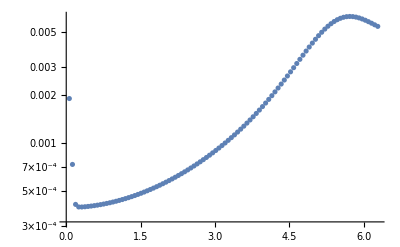

```mathematica
ΔtList=Table[(2.*π)/100 j,{j,1,100}];
ϵKList=ConstantArray[0,Length[ΔtList]];
Do[
Δt=ΔtList[[j]];
{Hmat,Smat}=funMatRTE[Λ,Eg,Δt,d,probφ];
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
err=EK-Eg;
ϵKList[[j]]=err;
,{j,1,Length[ΔtList]}]
Δt=ΔtList[[Position[ϵKList,Min[ϵKList]][[1,1]]]]
ListLogPlot[Transpose[{ΔtList,ϵKList}],PlotRange->Full]
```

```mathematica
E0=Eg;
{Hmat,Smat}=funMatRTE[Λ,E0,Δt,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
{ϵRTEList,γRTEList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵRTEList1,γRTEList1}=funEtaPracRTE[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListRTE,ϵListRTE}=funEpsilonMRTE[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Filter

```mathematica
τMIN=0;
τMAX=64;
While[True,
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatF[Λ,Eg,0,τ,1,probφ];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX}];*)
If[Abs[err-ϵB]<10^-10,Break[]];
];
τ
```

11.2447

0.02

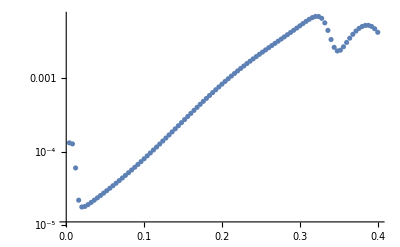

```mathematica
ΔEList=Table[2./(d*100)*j,{j,1,100}];
ϵKList=ConstantArray[0,Length[ΔEList]];
Do[(
ΔE=ΔEList[[j]];
{Hmat,Smat}=funMatF[Λ,Eg,ΔE,τ,d,probφ];
{EK,cn}=funSubDiag[Hmat+η*Id,Smat+η*Id];
err=EK-Eg;
ϵKList[[j]]=err;
),{j,1,Length[ΔEList]}]
ΔE=ΔEList[[Position[ϵKList,Min[ϵKList]][[1,1]]]]
ListLogPlot[Transpose[{ΔEList,ϵKList}],PlotRange->Full]
```

```mathematica
E0=Eg;
{Hmat,Smat}=funMatF[Λ,E0,ΔE,τ,d,probφ];
```

```mathematica
costH=1.;
costS=1.;
{ϵFList,γFList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
```

```mathematica
{ϵFList1,γFList1}=funEtaPracF[MList,rep,n,Hmat,Smat,d,κ,costH,costS,Id,Eg,pg];
```

```mathematica
{MListF,ϵListF}=funEpsilonM[Hmat,Smat,costH,costS,Id,ηList,Eg,d,κ];
```

## Plot

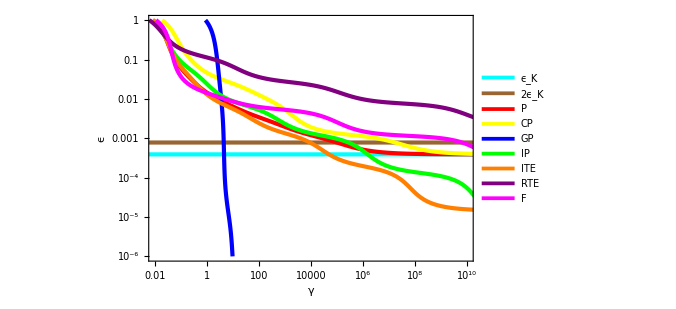

```mathematica
PR={{1.*^-2,1.*^10},{1.*^-6,1.*^0}};(*plot range*)
Fig=ListLogLogPlot[{Transpose[{γPList,0.*ϵPList+ϵK}],Transpose[{γPList,0.*ϵPList+2.*ϵK}],Transpose[{γPList,ϵPList}],Transpose[{γCPList,ϵCPList}],Transpose[{γGPList,ϵGPList}],Transpose[{γIPList,ϵIPList}],Transpose[{γITEList,ϵITEList}],Transpose[{γRTEList,ϵRTEList}],Transpose[{γFList,ϵFList}]},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.006],Cyan},{Thickness[0.006],Brown},{Thickness[0.006],Red},{Thickness[0.006],Yellow},{Thickness[0.006],Blue},{Thickness[0.006],Green},{Thickness[0.006],Orange},{Thickness[0.006],Purple},{Thickness[0.006],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"γ","ϵ"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"ϵ_K","2ϵ_K","P","CP","GP","IP","ITE","RTE","F"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",3}],{0.79,0.84}]]
```

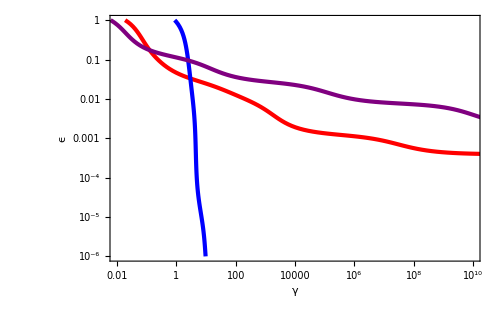

```mathematica
Fig1=ListLogLogPlot[{Transpose[{γCPList,ϵCPList}],Transpose[{γGPList,ϵGPList}],Transpose[{γRTEList,ϵRTEList}]},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.006],Red},{Thickness[0.006],Blue},{Thickness[0.006],Purple}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"γ","ϵ"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500]
```

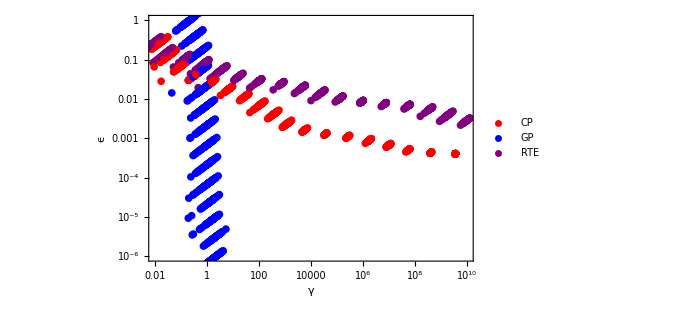

```mathematica
Fig2=Legended[Show[Table[ListLogLogPlot[{Transpose[{γCPList1[[i]],ϵCPList1[[i]]}],Transpose[{γGPList1[[i]],ϵGPList1[[i]]}],Transpose[{γRTEList1[[i]],ϵRTEList1[[i]]}]},PlotRange->PR,Joined->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"γ","ϵ"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotStyle->{Red,Blue,Purple}],{i,1,rep}]],Placed[PointLegend[{Red,Blue,Purple},{"CP","GP","RTE"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",3}],{0.77,0.86}]]
```

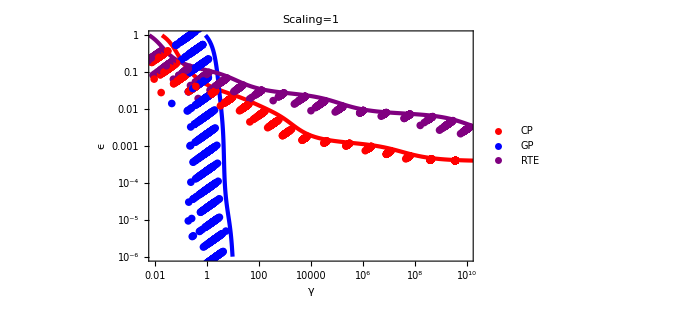

```mathematica
Fig3=Show[Fig1,Fig2,PlotLabel->"Scaling="<>ToString[n]]
```

```mathematica
(*path="C:\\Users\\John\\Desktop\\Revise\\practical eta-n="<>ToString[n]<>".pdf";
Export[path,Fig3];*)
```

## M vs epsilon with 1-kappa probability using eta_pract

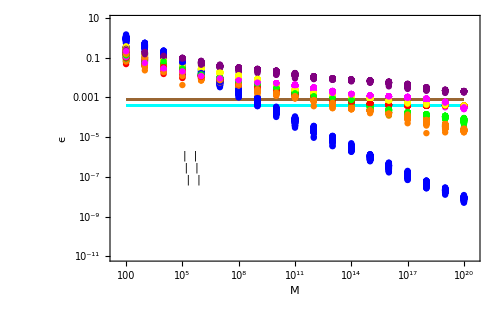

```mathematica
lleg1=LineLegend[{Cyan},{"ϵ_K"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
lleg2=LineLegend[{Brown},{"2ϵ_K"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg1=PointLegend[{Red},{"P"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg2=PointLegend[{Yellow},{"CP"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg3=PointLegend[{Blue},{"GP"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg4=PointLegend[{Green},{"IP"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg5=PointLegend[{Orange},{"ITE"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg6=PointLegend[{Purple},{"RTE"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
pleg7=PointLegend[{Magenta},{"F"},LegendMarkerSize->{14,7},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0];
Fig=
Legended[Show[Table[ListLogLogPlot[{Transpose[{MList,0.*MList+1.*ϵK}],Transpose[{MList,0.*MList+2.*ϵK}],Transpose[{MList,ϵPList1[[i]]}],Transpose[{MList,ϵCPList1[[i]]}],Transpose[{MList,ϵGPList1[[i]]}],Transpose[{MList,ϵIPList1[[i]]}],Transpose[{MList,ϵITEList1[[i]]}],Transpose[{MList,ϵRTEList1[[i]]}],Transpose[{MList,ϵFList1[[i]]}]},PlotRange->{{Min[MList]/3,Max[MList]*3},{Min[ϵGPList]/3,Max[ϵGPList]*3}},Joined->{True,True,False,False,False,False,False,False,False},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002],18],FrameLabel->{"M","ϵ"},LabelStyle->{FontSize->22,FontFamily->"Arial"},ImageSize->500,PlotStyle->{Cyan,Brown,Red,Yellow,Blue,Green,Orange,Purple,Magenta}],{i,1,rep}]],Placed[Grid[{{lleg1,pleg2,pleg5},{lleg2,pleg3,pleg6},{pleg1,pleg4,pleg7}},Alignment->Left,Frame->True,FrameStyle->LightGray],{{0.22,0.45},{0.5,1.5}}]]
```

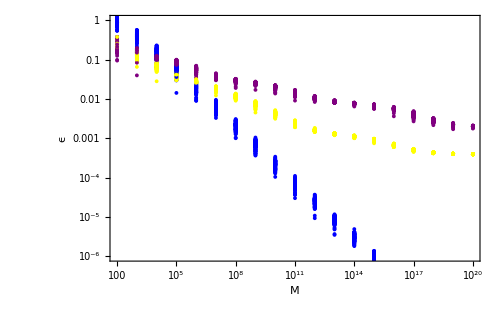

```mathematica
PR={{10^2,10^20},{10^-6,10^0}};(*plot range*)
Fig4=
Show[Table[ListLogLogPlot[{Transpose[{MList,ϵCPList1[[i]]}],Transpose[{MList,ϵGPList1[[i]]}],Transpose[{MList,ϵRTEList1[[i]]}]},PlotRange->PR,Joined->{False,False},PlotStyle->{{PointSize[0.0055],Yellow},{PointSize[0.0055],Blue},{PointSize[0.0055],Purple}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002],18],FrameLabel->{"M","ϵ"},LabelStyle->{FontSize->22,FontFamily->"Arial"},ImageSize->500],{i,1,rep}]]
```

```mathematica
ϵPListκ=funExtract[ϵPList1,MList,rep,κ];
ϵCPListκ=funExtract[ϵCPList1,MList,rep,κ];
ϵGPListκ=funExtract[ϵGPList1,MList,rep,κ];
ϵIPListκ=funExtract[ϵIPList1,MList,rep,κ];
ϵITEListκ=funExtract[ϵITEList1,MList,rep,κ];
ϵRTEListκ=funExtract[ϵRTEList1,MList,rep,κ];
ϵFListκ=funExtract[ϵFList1,MList,rep,κ];
```

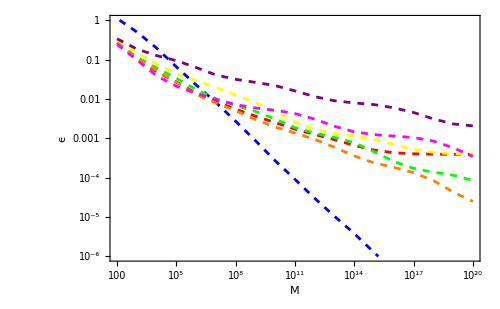

```mathematica
Fig5=ListLogLogPlot[{Transpose[{MList,ϵPListκ}],Transpose[{MList,ϵCPListκ}],Transpose[{MList,ϵGPListκ}],Transpose[{MList,ϵIPListκ}],Transpose[{MList,ϵITEListκ}],Transpose[{MList,ϵRTEListκ}],Transpose[{MList,ϵFListκ}]},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Red,Dashed},{Thickness[0.004],Yellow,Dashed},{Thickness[0.004],Blue,Dashed},{Thickness[0.004],Green,Dashed},{Thickness[0.004],Orange,Dashed},{Thickness[0.004],Purple,Dashed},{Thickness[0.004],Magenta,Dashed}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"M","ϵ"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500]
```

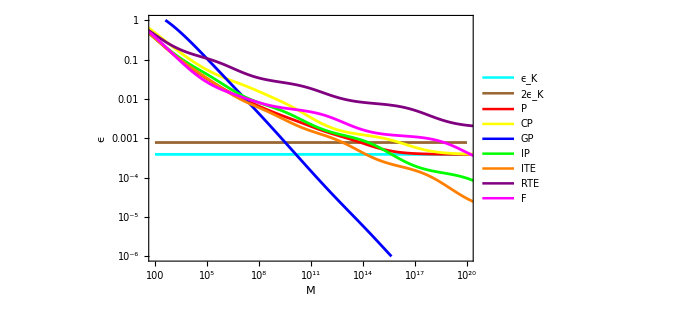

```mathematica
Fig6=ListLogLogPlot[{Transpose[{MList,0.*MList+1.*ϵK}],Transpose[{MList,0.*MList+2.*ϵK}],Transpose[{MListP,ϵListP}],Transpose[{MListCP,ϵListCP}],Transpose[{MListGP,ϵListGP}],Transpose[{MListIP,ϵListIP}],Transpose[{MListITE,ϵListITE}],Transpose[{MListRTE,ϵListRTE}],Transpose[{MListF,ϵListF}]},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.004],Cyan},{Thickness[0.004],Brown},{Thickness[0.004],Red},{Thickness[0.004],Yellow},{Thickness[0.004],Blue},{Thickness[0.004],Green},{Thickness[0.004],Orange},{Thickness[0.004],Purple},{Thickness[0.004],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"M","ϵ"},LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500,PlotLegends->Placed[LineLegend[{"ϵ_K","2ϵ_K","P","CP","GP","IP","ITE","RTE","F"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",3}],{0.79,0.84}]]
```

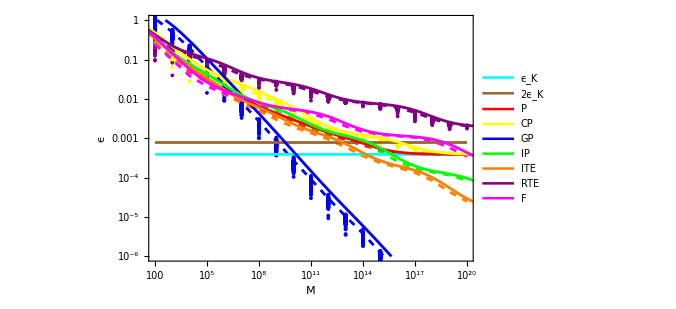

```mathematica
Fig7=Show[Fig4,Fig5,Fig6]
```

```mathematica
path="C:\\Users\\John\\Desktop\\Revise\\M-epsilon-Scaling="<>ToString[n]<>".pdf";
Export[path,Fig7];
```